```mathematica
H = p(a + b x^{1-η}/(1-η))δ[t]+ v(r*m-x+Subscript[ϕ, o] B(δ[t]/δInit)^γ)+ w*p
```

{p w+p (a+(b x^(1-η))/(1-η)) δ[t]+v (m r-x+B ϕ_o (δ[t]/δInit)^γ)}

```mathematica
Solve[D[H,x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(v/(b p δ[t]))^(-1/η)}}

```mathematica
xStar = (v/(b P δ[t]))^(-1/η)
```

(v/(b P δ[t]))^(-1/η)

```mathematica
D[H,m]
```

{r v}

```mathematica
D[H,p]
```

{w+(a+(b x^(1-η))/(1-η)) δ[t]}

```mathematica
DSolve[v'[t]==-r*v[t],v[t], t]
```

{{v[t]→ⅇ^(-r t) C[1]}}

```mathematica
DSolve[w'[t]== -(w[t]+(a+(b ((ⅇ^(-r t) C[1])/(b P δ[t]))^(1-η))/(1-η)) δ[t]),w[t],t]
```

{{w[t]→ⅇ^-t C[2]+ⅇ^-t -(ⅇ^(K[1]-r K[1]) ((ⅇ^(-r K[1]) C[1])/(b P δ[K[1]]))^-η (-C[1]-a ⅇ^(r K[1]) P ((ⅇ^(-r K[1]) C[1])/(b P δ[K[1]]))^η δ[K[1]]+a ⅇ^(r K[1]) P η ((ⅇ^(-r K[1]) C[1])/(b P δ[K[1]]))^η δ[K[1]]))/(P (-1+η))K[1]1t}}

```mathematica
DSolve[m'[t]== -r*m[t]- ((ⅇ^(-r t+ Integrate[δ[τ],{τ,0,t}]) C[1])/(b δ[t]))^(-1/η)+ϕ*B(δ[t]/δinit)^γ, m[t],t]
```

{{m[t]→ⅇ^(-r t) C[2]+ⅇ^(-r t) -ⅇ^(r K[1]) ((ⅇ^(∫_0^K[1] δ[τ]ⅆτ-r K[1]) C[1])/(b δ[K[1]]))^(-1/η) (1-B ϕ ((ⅇ^(∫_0^K[1] δ[τ]ⅆτ-r K[1]) C[1])/(b δ[K[1]]))^(1/η) (δ[K[1]]/δinit)^γ)K[1]1t}}

```mathematica
probas = {0.01, 0.10, 0.15,0.10, 0.20}
```

{0.01,0.1,0.15,0.1,0.2}

```mathematica
time = {2021,2029, 2040, 2060, 2100, 2500}
```

{2021,2029,2040,2060,2100,2500}

```mathematica
s = ConstantArray[0,Length[time]]
```

{0,0,0,0,0,0}

```mathematica
s[[1]]=1
```

1

```mathematica
For[i=1, i<Length[time],i++,s[[i+1]]=(1-probas[[i]])*s[[i]]]
```

```mathematica
s
```

{1,0.99,0.891,0.75735,0.681615,0.545292}

```mathematica
survival = {time, s}
```

{{2021,2029,2040,2060,2100,2500},{1,0.99,0.891,0.75735,0.681615,0.545292}}

```mathematica
survival
```

{{2021,2029,2040,2060,2100,∞},{1,0.99,0.891,0.75735,0.681615,0.545292}}

```mathematica
{{2021,2029,2040,2060,2100,∞},{1,0.99,0.891,0.75735,0.681615,0.545292}}
```

{{2021,2029,2040,2060,2100,∞},{1,0.99,0.891,0.75735,0.681615,0.545292}}

```mathematica
survival = Table[0, Length[s],2]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}
 survival[[1]][[1]]=time[[1]];  survival[[1]][[2]]=s[[i]]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

0.545292

```mathematica
survival
```

{{2021,0.545292},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
{{2021,1,2040,2060,2100,2500},{2029,0.99,0.891,0.75735,0.681615,0.545292}}
```

```mathematica
For[i=1, i<Length[time],i++,survival[[i]][[1]]=time[[i]];  survival[[i]][[2]]=s[[i]]]
```

```mathematica
survival
```

```mathematica
{{2021,1},{2029,0.99},{2040,0.891},{2060,0.75735},{2100,0.681615},{0,0}}
survivial={{2021,1},{2029,0.99},{2040,0.891},{2060,0.75735},{2100,0.681615}}
```

{{2021,1},{2029,0.99},{2040,0.891},{2060,0.75735},{2100,0.681615},{0,0}}

{{2021,1},{2029,0.99},{2040,0.891},{2060,0.75735},{2100,0.681615}}

```mathematica
pSurvival = Interpolation[survival]
```

InterpolatingFunction[…]

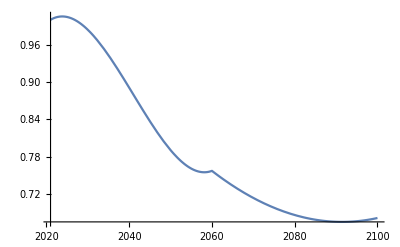

```mathematica
InterpolatingFunction[…]
Plot[pSurvival[t], {t,2021, 2100}]
```

```mathematica
pSurvival = Interpolation[{{2021,1},{2029,0.99},{2040,0.891},{2060,0.75735},{2100,0.681615}}]
```

InterpolatingFunction[…]

```mathematica
pSurvival
```

InterpolatingFunction[…]

```mathematica
D[pSurvival]
```

```mathematica
InterpolatingFunction[…]
Plot[pSurvival,{x,2021,2100}]
```

InterpolatingFunction[…]

-Graphics-

```mathematica
pSurvival
```

InterpolatingFunction[…]

```mathematica
pSurvival[2050]
```

0.79071

```mathematica
pSurvival[2080]
```

0.686415

```mathematica
pSurvival[2070]
```

0.713829

```mathematica
pSurvival[2100]
```

0.681615

```mathematica
pSurvival[2200]
```

InterpolatingFunction::dmval: Input value {2200} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.7694

```mathematica
Plot[pSurvival[t], {t,2021, 2100}]
```

-Graphics-

```mathematica
delta =- D[pSurvival[t],t]/pSurvival[t]
```

-(InterpolatingFunction[…][t])/(InterpolatingFunction[…][t])

```mathematica
InterpolatingFunction[…][t]
```

InterpolatingFunction[…][t]

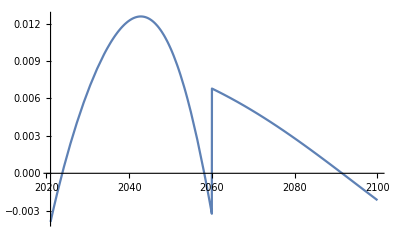

```mathematica
Plot[delta, {t,2021, 2100}]
```

```mathematica
time = {2021,2029,2040,2060,2100,2500}
```

{2021,2029,2040,2060,2100,2500}

```mathematica
s = {1,0.99,0.891,0.75735,0.681615,0.545292}
```

```mathematica
{1,0.99,0.891,0.75735,0.681615,0.545292}
```

```mathematica
pS= ConstantArray[0,Length[time]]
```

```mathematica
{0,0,0,0,0,0}
Clear[pS]
```

{0,0,0,0,0,0}

```mathematica
For[i=1, i<Length[time],i++,pS[i,t]= (s[[i+1]]-s[[i]])/(time[[i+1]]-time[[i]])*(t-time[[i]]) + s[[i]]]
```

```mathematica
pS[1,t]
```

1-0.00125 (-2021+t)

```mathematica
condition =  ConstantArray[0,Length[time]-1]
```

```mathematica
{0,0,0,0,0}
Clear[condition]
```

{0,0,0,0,0}

```mathematica
For[i=1, i<Length[time],i++,condition[i,t] = time[[i]]<=t< time[[i+1]]]
```

```mathematica
condition[1,t]
```

2021≤t<2029

```mathematica
Clear[survivialGraph]
survivialGraph[t_] :=
```

```mathematica
survivialGraph[2][[1]][[2]]
```

```mathematica
survivialGraph[t][[1]][[1]]
```

```mathematica
Clear[survivalGraph]
```

```mathematica
survivalGraph = ConstantArray[t,{Length[time]-1,2 }]
```

{{t,t},{t,t},{t,t},{t,t},{t,t}}

```mathematica
For[i=1, i<=Length[time]-1,i++,survivalGraph[[i]][[1]] = pS[i,t]; survivalGraph[[i]][[2]]= condition[i,t]]
survivalGraph
```

{{1-0.00125 (-2021+t),2021≤t<2029},{0.99-0.009 (-2029+t),2029≤t<2040},{0.891-0.0066825 (-2040+t),2040≤t<2060},{0.75735-0.00189338 (-2060+t),2060≤t<2100},{0.681615-0.000340807 (-2100+t),2100≤t<2500}}

General::stop: Further output of Set::noval will be suppressed during this calculation.

Set::noval: Symbol survivalGraph in part assignment does not have an immediate value.

General::stop: Further output of Set::setps will be suppressed during this calculation.

Set::setps: survivalGraph[t] in the part assignment is not a symbol.

General::stop: Further output of StyleBox[RowBox[{\"Set\", \"::\", \"setps\"}], \"MessageName\"] will be suppressed during this calculation.

Part::partd: Part specification survivialGraph⟦1⟧ is longer than depth of object.

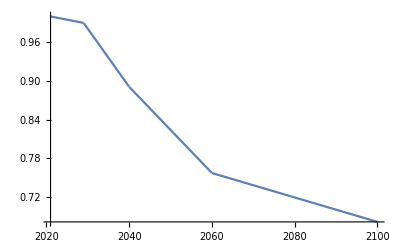

```mathematica
Plot[Piecewise[survivalGraph],{t,2021,2100}]
```

```mathematica
Clear[δ]
```

```mathematica
δ= - D[Piecewise[survivalGraph],t]/Piecewise[survivalGraph]
```

-Piecewise[{{0, t<2021}, {-0.00125, 2021<t<2029}, {-0.009, 2029<t<2040}, {-0.0066825, 2040<t<2060}, {-0.00189338, 2060<t<2100}, {-0.000340807, 2100<t<2500}, {0, t>2500}, {Indeterminate, True}}]/Piecewise[{{1-0.00125 (-2021+t), 2021≤t<2029}, {0.99-0.009 (-2029+t), 2029≤t<2040}, {0.891-0.0066825 (-2040+t), 2040≤t<2060}, {0.75735-0.00189338 (-2060+t), 2060≤t<2100}, {0.681615-0.000340807 (-2100+t), 2100≤t<2500}, {0, True}}]

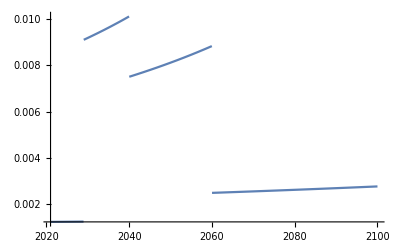

```mathematica
Plot[δ, {t,2021, 2100}]
```

```mathematica
H = p(a + b x^{1-η}/(1-η))δ+ v(r*m-x+Subscript[ϕ, o] B(δ/δInit)^γ)+ w*p
```

{p w-(p (a+(b x^(1-η))/(1-η)) (Piecewise[{{0, t<2021}, {-0.00125, 2021<t<2029}, {-0.009, 2029<t<2040}, {-0.0066825, 2040<t<2060}, {-0.00189338, 2060<t<2100}, {-0.000340807, 2100<t<2500}, {0, t>2500}, {Indeterminate, True}}]))/Piecewise[{{1-0.00125 (-2021+t), 2021≤t<2029}, {0.99-0.009 (-2029+t), 2029≤t<2040}, {0.891-0.0066825 (-2040+t), 2040≤t<2060}, {0.75735-0.00189338 (-2060+t), 2060≤t<2100}, {0.681615-0.000340807 (-2100+t), 2100≤t<2500}, {0, True}}]+v (m r-x+B (-Piecewise[{{0, t<2021}, {-0.00125, 2021<t<2029}, {-0.009, 2029<t<2040}, {-0.0066825, 2040<t<2060}, {-0.00189338, 2060<t<2100}, {-0.000340807, 2100<t<2500}, {0, t>2500}, {Indeterminate, True}}]/(δInit (Piecewise[{{1-0.00125 (-2021+t), 2021≤t<2029}, {0.99-0.009 (-2029+t), 2029≤t<2040}, {0.891-0.0066825 (-2040+t), 2040≤t<2060}, {0.75735-0.00189338 (-2060+t), 2060≤t<2100}, {0.681615-0.000340807 (-2100+t), 2100≤t<2500}, {0, True}}])))^γ ϕ_o)}

```mathematica
DSolve[m'[t]== -r*m[t]- ((ⅇ^(-r t+ δInt/.T->t) C[1])/(b δ))^(-1/η)+ϕ*B(δ/δinit)^γ, m[t],{t,2021,2500}]
```

Integrate::pwrl: Unable to prove that integration limits {0,t} are real. Adding assumptions may help.

General::stop: Further output of Integrate::pwrl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0 ComplexInfinity)/δinit encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0 ComplexInfinity)/δinit encountered.

```mathematica
δInt = Integrate[δ,{t,2021,T},Assumptions->2021<T≤2500]
```

```mathematica
Piecewise[{{0.38329029666692893+Log[(6.181708400000001*^15)/(1.267250222*^16-3.0908542*^12 T)], 2100.<T≤2500.}, {6.10687539861931-1. Log[6520.-3. T], 2040.<T≤2060.}, {Log[-800./(-2821.+T)], 2021.<T≤2029.}, {0.27792978100910265+Log[-400./(-2460.+T)], 2060.<T≤2100.}, {0.010050335853501442+Log[-110./(-2139.+T)], True}}]
```

```mathematica
δint = δInt/.T->t
```

Piecewise[{{0.38329+Log[(6.18171×10^15)/(1.26725×10^16-3.09085×10^12 t)], 2100.<t≤2500.}, {6.10688-1. Log[6520.-3. t], 2040.<t≤2060.}, {Log[-800./(-2821.+t)], 2021.<t≤2029.}, {0.27793+Log[-400./(-2460.+t)], 2060.<t≤2100.}, {0.0100503+Log[-110./(-2139.+t)], True}}]

Piecewise[{{0.38329+Log[(6.18171×10^15)/(1.26725×10^16-3.09085×10^12 T)], 2100.<T≤2500.}, {6.10688-1. Log[6520.-3. T], 2040.<T≤2060.}, {Log[-800./(-2821.+T)], 2021.<T≤2029.}, {0.27793+Log[-400./(-2460.+T)], 2060.<T≤2100.}, {0.0100503+Log[-110./(-2139.+T)], True}}]

```mathematica
δ/.t->t
```

-Piecewise[{{0, t<2021}, {-0.00125, 2021<t<2029}, {-0.009, 2029<t<2040}, {-0.0066825, 2040<t<2060}, {-0.00189338, 2060<t<2100}, {-0.000340807, 2100<t<2500}, {0, t>2500}, {Indeterminate, True}}]/Piecewise[{{1-0.00125 (-2021+t), 2021≤t<2029}, {0.99-0.009 (-2029+t), 2029≤t<2040}, {0.891-0.0066825 (-2040+t), 2040≤t<2060}, {0.75735-0.00189338 (-2060+t), 2060≤t<2100}, {0.681615-0.000340807 (-2100+t), 2100≤t<2500}, {0, True}}]

```mathematica
δint[t]=Piecewise[{{0.38329029666692893+Log[(6.181708400000001*^15)/(1.267250222*^16-3.0908542*^12 t)], 2100.<t≤2500.}, {6.10687539861931-1. Log[6520.-3. t], 2040.<t≤2060.}, {Log[-800./(-2821.+t)], 2021.<t≤2029.}, {0.27792978100910265+Log[-400./(-2460.+t)], 2060.<t≤2100.}, {0.010050335853501442+Log[-110./(-2139.+t)], 2029.<t≤2040.}, {0., t≤2021.}, {Indeterminate, True}}]
```

Piecewise[{{0.38329+Log[(6.18171×10^15)/(1.26725×10^16-3.09085×10^12 t)], 2100.<t≤2500.}, {6.10688-1. Log[6520.-3. t], 2040.<t≤2060.}, {Log[-800./(-2821.+t)], 2021.<t≤2029.}, {0.27793+Log[-400./(-2460.+t)], 2060.<t≤2100.}, {0.0100503+Log[-110./(-2139.+t)], 2029.<t≤2040.}, {0., t≤2021.}, {Indeterminate, True}}]

```mathematica
δint[t]
```

Piecewise[{{0.38329+Log[(6.18171×10^15)/(1.26725×10^16-3.09085×10^12 t)], 2100.<t≤2500.}, {6.10688-1. Log[6520.-3. t], 2040.<t≤2060.}, {Log[-800./(-2821.+t)], 2021.<t≤2029.}, {0.27793+Log[-400./(-2460.+t)], 2060.<t≤2100.}, {0.0100503+Log[-110./(-2139.+t)], 2029.<t≤2040.}, {0., t≤2021.}, {Indeterminate, True}}]

```mathematica
f[x] = Piecewise[{{-1, x>=0},{-2,x<0}}]
```

Piecewise[{{-1, x≥0}, {-2, x<0}, {0, True}}]

```mathematica
sol = NDSolve[{y'[x]==-r*y[x]+g*f[x]/.r->0.05/.g->0.10, y[0]==1},y,{x,-20,20}]
```

{{y→InterpolatingFunction[…]}}

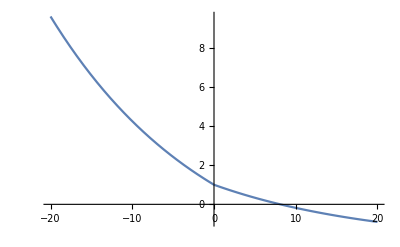

```mathematica
Plot[y[x]/.sol,{x,-20,20}]
```

```mathematica
NDSolve[{m'[t]== -r*m[t]- ((ⅇ^(-r t+ δInt/.T->t) C[1])/(b (δ/.t->t)))^(-1/η)+ϕ*B((δ/.t->t)/δinit)^γ/.r->0.05/.ϕ->0.10/.B->100/.δinit->0.0020/.γ->5/.η->2/.b->1/.C[1]->1, m[0]==100},m,{t,2021,2500}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^5 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{m'[t]==-0.05 m[t]-1/(√(-(ⅇ^(-0.05 t+(Piecewise[{{0.38329+Log[(6.18171×10^15)/(1.26725×10^16-3.09085×10^12 t)], 2100.<t≤2500.}, {6.10688-1. Log[6520.-3. t], 2040.<t≤2060.}, {Log[-800./(-2821.+t)], 2021.<t≤2029.}, {0.27793+Log[-400./(-2460.+t)], 2060.<t≤2100.}, {0.0100503+Log[-110./(-2139.+t)], True}}])) (Piecewise[{{1-0.00125 (-2021+t), 2021≤t<2029}, {0.99-0.009 (-2029+t), 2029≤t<2040}, {0.891-0.0066825 (-2040+t), 2040≤t<2060}, {0.75735-0.00189338 (-2060+t), 2060≤t<2100}, {0.681615-0.000340807 (-2100+t), 2100≤t<2500}, {0, True}}]))/Piecewise[{{0, t<2021}, {-0.00125, 2021<t<2029}, {-0.009, 2029<t<2040}, {-0.0066825, 2040<t<2060}, {-0.00189338, 2060<t<2100}, {-0.000340807, 2100<t<2500}, {0, t>2500}, {Indeterminate, True}}]))-(3.125×10^14 (Piecewise[{{0, t<2021}, {-0.00125, 2021<t<2029}, {-0.009, 2029<t<2040}, {-0.0066825, 2040<t<2060}, {-0.00189338, 2060<t<2100}, {-0.000340807, 2100<t<2500}, {0, t>2500}, {Indeterminate, True}}])^5)/(Piecewise[{{1-0.00125 (-2021+t), 2021≤t<2029}, {0.99-0.009 (-2029+t), 2029≤t<2040}, {0.891-0.0066825 (-2040+t), 2040≤t<2060}, {0.75735-0.00189338 (-2060+t), 2060≤t<2100}, {0.681615-0.000340807 (-2100+t), 2100≤t<2500}, {0, True}}])^5,m[0]==100},m,{t,2021,2500}]

```mathematica
-r*m[t]- ((ⅇ^(-r t+ δInt/.T->t) C[1])/(b (δ/.t->t)))^(-1/η)+ϕ*B((δ/.t->t)/δinit)^γ/.r->0.05/.ϕ->0.10/.B->100/.δinit->0.0020/.γ->5/.η->2/.b->1/.C[1]->1
```

-0.05 m[t]-1/(√(-(ⅇ^(-0.05 t+(Piecewise[{{0.38329+Log[(6.18171×10^15)/(1.26725×10^16-3.09085×10^12 t)], 2100.<t≤2500.}, {6.10688-1. Log[6520.-3. t], 2040.<t≤2060.}, {Log[-800./(-2821.+t)], 2021.<t≤2029.}, {0.27793+Log[-400./(-2460.+t)], 2060.<t≤2100.}, {0.0100503+Log[-110./(-2139.+t)], True}}])) (Piecewise[{{1-0.00125 (-2021+t), 2021≤t<2029}, {0.99-0.009 (-2029+t), 2029≤t<2040}, {0.891-0.0066825 (-2040+t), 2040≤t<2060}, {0.75735-0.00189338 (-2060+t), 2060≤t<2100}, {0.681615-0.000340807 (-2100+t), 2100≤t<2500}, {0, True}}]))/Piecewise[{{0, t<2021}, {-0.00125, 2021<t<2029}, {-0.009, 2029<t<2040}, {-0.0066825, 2040<t<2060}, {-0.00189338, 2060<t<2100}, {-0.000340807, 2100<t<2500}, {0, t>2500}, {Indeterminate, True}}]))-(3.125×10^14 (Piecewise[{{0, t<2021}, {-0.00125, 2021<t<2029}, {-0.009, 2029<t<2040}, {-0.0066825, 2040<t<2060}, {-0.00189338, 2060<t<2100}, {-0.000340807, 2100<t<2500}, {0, t>2500}, {Indeterminate, True}}])^5)/(Piecewise[{{1-0.00125 (-2021+t), 2021≤t<2029}, {0.99-0.009 (-2029+t), 2029≤t<2040}, {0.891-0.0066825 (-2040+t), 2040≤t<2060}, {0.75735-0.00189338 (-2060+t), 2060≤t<2100}, {0.681615-0.000340807 (-2100+t), 2100≤t<2500}, {0, True}}])^5

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0 ComplexInfinity)/δinit encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0 ComplexInfinity)/δinit encountered.

```mathematica
sol = NDSolve[{y'[x]==-r*y[x]+g*f[x]/.{r->0.05,g->0.10}, y[0]==1},y,{x,-20,20}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Plot[y[x]/.sol,{x,-20,20}]
```

-Graphics-